# Mimicking Tweets

## Jeffrey Starr - 2013 October 04

## Data Source

Previously, in the TextualPatternsInTweets notebook, we generated frequency tables based on tweets. The tables below consist of n+1 tuples, with the first n entries representing characters found in tweets and the final entry representing the count found (an integer greater than or equal to one).

```mathematica
n2table=Import["Data/n2table.json",CharacterEncoding->"UTF8"];
```

```mathematica
n3table=Import["Data/n3table.json",CharacterEncoding->"UTF8"];
```

```mathematica
n4table=Import["Data/n4table.json",CharacterEncoding->"UTF8"];
```

Hmm... I can’t load n5table directly; there is an recusion limit and out of memory error in the underlying Java-based JSON parser.

```mathematica
n5table=Import["Data/n5table.csv",CharacterEncoding->"UTF8"];
```

$CharacterEncoding::utf8: The byte sequence {240} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {159} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {152} could not be interpreted as a character in the UTF-8 character encoding.

General::stop: Further output of $CharacterEncoding :: utf8 will be suppressed during this calculation.

```mathematica
n5table=DeleteCases[n5table,Except[{_String,_Integer}]];
```

```mathematica
Length[n5table]
```

390313

```mathematica
n9table=Import["Data/n9table.csv",CharacterEncoding->"UTF8"];
```

$CharacterEncoding::utf8: The byte sequence {240} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {159} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {152} could not be interpreted as a character in the UTF-8 character encoding.

General::stop: Further output of $CharacterEncoding :: utf8 will be suppressed during this calculation.

```mathematica
n9table=DeleteCases[n9table,Except[{_String,_Integer}]];
```

```mathematica
Length[n9table]
```

906612

```mathematica
n12table=Import["Data/n12table.csv",CharacterEncoding->"UTF8"];
```

$CharacterEncoding::utf8: The byte sequence {240} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {159} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {152} could not be interpreted as a character in the UTF-8 character encoding.

General::stop: Further output of $CharacterEncoding :: utf8 will be suppressed during this calculation.

```mathematica
n12table=DeleteCases[n12table,Except[{_String,_Integer}]];
```

```mathematica
Length[n12table]
```

1036454

## Condensing Tables

Treating each character as a separate item in the list is wasteful. Let’s convert them to 2-tuples, with the first entry be a string with n characters.

```mathematica
Collapse[table_]:=
Table[
{StringJoin[table[[record]][[1;;Length[table[[record]]]-1]]],table[[record]][[-1]]},
{record,Length[table]}
]
```

```mathematica
n2table=Collapse[n2table];
```

```mathematica
n3table=Collapse[n3table];
```

```mathematica
n4table=Collapse[n4table];
```

n5table is already collapsed.

## Weight List

When we choose an entry by random, we need to make the choice with respect to the existing probabilities. In Mathematica, we use the function RandomChoice which expects input in the form {w_1,w_2,…}->{e_1,e_2,…}.

```mathematica
ToWeightList[list_]:=
(Last/@list)->(First/@list)
```

## Generating Text

To simplify the API, two global variables:

```mathematica
𝔗=n3table; (* table reference *)
𝔑=StringLength[𝔗[[1]][[1]]]; (* number of characters in string *)
```

```mathematica
Seed[]:=RandomChoice[ToWeightList[𝔗]]
```

To initiate a text, we first choose an entry at random. This is the seed.

Once we have a seed (or text that has built upon the seed), we can add a letter to the text by looking a the n-1 characters from our table and choosing the next probabilistically.

```mathematica
NextLetters[text_String]:=
Select[𝔗,StringMatchQ[#[[1]],StringTake[text,-𝔑+1]~~_]&]/.{s_String,w_Integer}:>{StringTake[s,-1],w}
```

Given the text so far, return the text plus at least one character.

```mathematica
ChooseNext[text_String]:=
Module[
{nls=NextLetters[text]},
Switch[nls,
{},
StringJoin[text,Seed[]],
_,
StringJoin[text,RandomChoice[ToWeightList[nls]]]
]
]
```

## Example Generation

### n=3

```mathematica
𝔗=n3table;
𝔑=StringLength[𝔗[[1]][[1]]];
```

```mathematica
Column[
Table[
Nest[ChooseNext,Seed[],30],
{10}
],
Frame->All
]
```

6 me banshou tweded HURT @oui: I 
odur our itto chapposeeknowspass 
_que-se.Yore!!!! houst usias th t
o dif able forthe whine aspre On 
and penreekins_ @ouldri @on a ar 
roursomemy ar en ithellbyFan http
stude... ❤ ❤ ❤ ❤✌ on I… hamilaut 
atersto gasequally Tictince Hom c
 | MERE Bry, tomed 5: Itz: @ ohtt
y we fole wit ittink &ame justur

### n=4

```mathematica
𝔗=n4table;
𝔑=StringLength[𝔗[[1]][[1]]];
```

```mathematica
Column[
ParallelTable[
Nest[ChooseNext,Seed[],30],
{10}
],
Frame->All
]
```

U MONE? I far is me sing LikeJohnn
y: Thats best Mar0tte to Gla… Middodr
s to Down and and Go Britisiter tw
yn Halfd to suren_ @o a kiddlovers
llo97 whool I WAS THE OF THEY #cam
 andthe LET'S AND I aciet as Some.
ed to get with kick his us an You 
" Luke: i way?.. El Dont, built lo
ation. (Re)-straigestill could I c
ed it's Clasten. Welcore #Frentshu

### n=5

```mathematica
𝔗=n5table;
𝔑=StringLength[𝔗[[1]][[1]]];
```

```mathematica
Column[
ParallelTable[
Nest[ChooseNext,Seed[],30],
{10}
],
Frame->All
]
```

mishopper_: makes tho &lt;&lt;3 CA
solute their to get wonde :)x I get
m1345://t.co/2GXdLx0fW2 via @Lilia_rmz:
post "Wreckless is dey hurt I said 
ght wing peace Tell message really 
x5HRu us to stats: No next me followed 
' over 5sos almost into far upset a
anz: Some I'm wait--it's become sea
 not get up &amp; Shiieel soon. #En
ng for a Duval in dem when I'm not

### n=9

```mathematica
𝔗=n9table;
𝔑=StringLength[𝔗[[1]][[1]]];
```

```mathematica
Column[
ParallelTable[
Nest[ChooseNext,Seed[],30],
{10}
],
Frame->All
]
```

A Cop ð.9f.98.8e:d83dapping in fellaake: so far we get the champion
oncentration Falsifying Federal Retail 
sleep TW…l talk to me at booth 125 and 670! htt
a wizard crib for the follow or tweet #
abb_sanchez: Want Vs. Need #TheStruggle
sx awwww thank you poop, thank YOU! It 
on the floor …opped my iPhone 5c! Join to win! 
heart: I meet One Direction is gonna st
ng anything else is just inside.. She w
e, but FAITH is what happens , happen t

### n=12

```mathematica
𝔗=n12table;
𝔑=StringLength[𝔗[[1]][[1]]];
```

```mathematica
Column[
ParallelTable[
Nest[ChooseNext,Seed[],30],
{10}
],
Frame->All
]
```

ies I CA NT BREATHE http://t.co/YS0toh0VZ…
hink the point where we realize we’ve... h
how did I know ? :d83dion and Asset Coverage Ratio Upd...
ly feel ugly bc thats me today oh wait tha
 my days off ! Hit a few golf balls from m
her &amp; allows me to feel like the least
r: I support a Canadian.co/EPxtkMWipZast: Ima go eat some food"f
bestboobs @TitsTatsAssKink http://t.co/Nfj
indeer gameshkartini @nyaa026 @desdesidess @soniabsm 
HATS A LOT :d83chi @"y Way over there? predictions somehow came through.

```mathematica
Column[
ParallelTable[
Nest[ChooseNext,Seed[],30],
{10}
],
Frame->All
]
```

ingEDM: The sun hits like a bullet of fait
ES YOU #camilacafollowspree @camilacabello
age when the sun is starting this month my
tness #beverages #drinking #lifestyleK, kids who cut 
ng and shit :D hahaha @SMistry_ lie in tomorrow in a 
hanelpuke: my rapper name would be A1 righ
ats Behind Luis Suarez made his long antic
y the same person twice. Becomes a prob wh
BTHEBASEDGOD @GirlTimeUSA You're  very bea
gh key hate Steviess you think is funny but everyone

## Huffman Encoding

NextLetters[] returns a frequency table -- a list of token, # of occurences tuples. (The input tables are also frequency tables.) Frequency tables can be encoded as a binary tree using Huffman encoding. Later, we will use the path transversal of the tree to encode and decode messages.

Introduction to Algorithms, Second Edition by Cormen, et al., describes the Huffman algorithm on page 388 as:
n<-|C|
Q<-C
for i <-1 to n-1
	do allocate a new node z
		left[z] <- x <- Extract-Min(Q)
		right[z] <- y <- Extract-Min(Q)
		f[z] <- f[x] + f[y]
		Insert(Q, z)
return Extract-Min(Q)

First, we define the user-end of the Huffman algorithm. It takes a list of 2-tuples, with the weight or frequency as the second element in the tuples.

```mathematica
Huffman[freqlist_]:=
Switch[freqlist,
{},
{} (*Print["Request to Huffman an empty list"];
Abort[]*),
_List,
HuffmanQ[Sort[freqlist,#1[[2]]<#2[[2]]&]/.{t_String,w_Integer}->{Null,t,w,Null}],
_,
Print["Request to Huffman a non-list: ",freqlist];
Abort[]
]
```

If the priority queue is empty, return the empty list.

```mathematica
HuffmanQ[{}]:={}
```

If the priority queue has only a single element, return the head.

```mathematica
HuffmanQ[{{l_,t_,w_,r_}}]:={l,t,w,r}
```

For all other cases (length of the queue ≥2), apply the function recursively.

```mathematica
HuffmanQ[Q_]:=
If[(Length[Q[[1]]]≠4)∨(Length[Q[[2]]]≠4),
Print["Q[[1]]: ",Length[Q[[1]]]," ",Q[[1]]];
Print["Q[[2]]: ", Length[Q[[2]]]," ",Q[[2]]];
Print["Q     : ",Length[Q]," ",Q];
InputForm[Q];
Abort[];,
With[
{left=Q[[1]],
right=Q[[2]],
fz=Q[[1]][[3]]+Q[[2]][[3]]},
If[Length[Q]≥3,
HuffmanQ[
Insert[
Q[[3;;]],
{left,"",fz,right},
SortedPosition[Q[[3;;]],fz]
]
],
HuffmanQ[{{left,"",fz,right}}]
]
]
]
```

SortedPosition returns the position in list Q for w.

```mathematica
SortedPosition[Q_,w_Integer]:=
SortedPosition[Q,w,1]
```

```mathematica
SortedPosition[Q_,w_Integer,n_Integer]:=
If[n>Length[Q],n,
If[Length[Q[[n]]]==4,
(* Q is correctly formatted with a 4-tuple *)
If[w>Q[[n]][[3]],n,
SortedPosition[Q,w,n+1]
],
(* else, Q is incorrectly formatted *)
Print["Q[[n]] is not a 4-tuple: ",Q[[n]]];
Print[Stack[]];
Abort[];
]
]
```

```mathematica
𝔗=n3table; (* table reference *)
𝔑=StringLength[𝔗[[1]][[1]]]; (* number of characters in string *)
```

```mathematica
fl3=NextLetters["~~~"];
```

```mathematica
NextLetters["~~~"]
```

{{~,8},{#,1},{ ,1},{&,1},{S,1}}

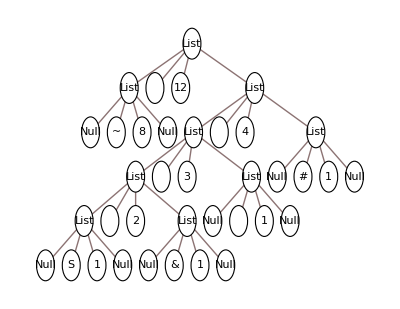

```mathematica
TreeForm[
Huffman[fl3],
Infinity,
VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.2],Black,Text[#2,#1]}&)
]
```

## Steganographic Encryption

Let a transversal to the left represent 0 and a transversal to the right represent 1. Then, given a Huffman tree and a binary string, return a token from the tree and the unused binary characters.

```mathematica
HuffmanEncode[htree_,{}]:=
Switch[htree[[2]],
"",(* non-terminal node in tree *)
HuffmanEncode[htree[[1]],{}], (* effectively pad zeros if no further digits to encode *)
_String, (* reached terminal character *)
{htree[[2]],{}}
]
```

```mathematica
HuffmanEncode[htree_,binarylist_]:=
Switch[htree[[2]],
"",(* non-terminal node in tree *)
Switch[First[binarylist],
0,
HuffmanEncode[htree[[1]],Rest[binarylist]],
1,
HuffmanEncode[htree[[4]],Rest[binarylist]],
_,
Print["Found non-binary digit ",Head[binarylist]," in binarylist"];
Abort[]
],
_String,(* reached terminal character *)
{htree[[2]],binarylist} ,
_,
Print["Found non-string character/empty string in htree"];
Abort[] (* should not reach *)
]
```

```mathematica
HuffmanEncode[Huffman[fl3],{1,0,0,1}]
```

{&,{}}

```mathematica
HuffmanEncode[Huffman[fl3],{1,1,0,0,1,0,0,1}]
```

{#,{0,0,1,0,0,1}}

```mathematica
HuffmanEncode[Huffman[fl3],{0,0,1,0,0,1}]
```

{~,{0,1,0,0,1}}

```mathematica
HuffmanEncode[Huffman[fl3],{0,1,0,0,1}]
```

{~,{1,0,0,1}}

```mathematica
HuffmanEncode[Huffman[fl3],{1,0,0,1}]
```

{&,{}}

Not all strings can be successfully encoded because not all transversals lead to terminal nodes. However, all paths eventually reach a terminal node. We can modify the algorithm to pad zeros as necessary.

```mathematica
HuffmanEncode[Huffman[fl3],{1}]
```

First::first: {} has a length of zero and no first element.

Found non-binary digit List in binarylist

$Aborted

```mathematica
HuffmanEncode[Huffman[fl3],{1}]
```

{S,{}}

Given a string result so far and a list of binary digits, return a 2-tuple of the result with appended encoded characters and remaining inbits.

```mathematica
HuffmanEncodeIter[result_,inbits_]:=
With[
{nls=NextLetters[result]},
Switch[nls,
{},
HuffmanEncodeIter[StringJoin[result,Seed[]],inbits],
_,
With[{q=HuffmanEncode[Huffman[nls],inbits]},
{StringJoin[result,q[[1]]],q[[2]]}]
]
]
```

```mathematica
HuffmanEncodeIter["text so far", {1,1,0,0,1,0,0,1}]
```

{text so farbaab,{1,0,0,1,0,0,1}}

Takes a string and returns a list of binary digits (integer zero and one) based on the 16-bit (UTF-16) decoding of each character. JavaScript’s charCodeAt is 16-bit, so the two versions should be compatible.

```mathematica
ToBinaryString[plaintext_]:=
Flatten[
IntegerDigits[ToCharacterCode[#],2,16]&/@StringSplit[plaintext,""]
]
```

Note: compressing the binary string represenation of plaintext would be a good idea; particularly as there are long sections of padded zeros for most English text.

Encode takes plaintext, a global link to a ntable, and then: transforms plaintext to a binary string, seeds the output text, iteratively generates a frequency table for the next character choices given the output text until all the binary plain text is consumed.

```mathematica
StegEncrypt[plaintext_]:=
First[
NestWhile[
HuffmanEncodeIter[#[[1]],#[[2]]]&,
{Seed[],ToBinaryString[plaintext]} (* add to out, consume in *),
Length[#[[2]]]>0&
]
]
```

### n=3

These examples are generated using third-order text.

```mathematica
𝔑
```

3

```mathematica
StegEncrypt["hello"]//Timing
```

{6.84443,milowsprostionlow: I wqn ty}

```mathematica
StegEncrypt["helloworld"]//Timing
```

{12.22876,s smilaways bby llocke t- hinigh t- hople ptS}

```mathematica
StegEncrypt["To be, or not to be."] //Timing
```

{23.59747,o museet.… sond c'moody to wasablver." - 1,77 #bf t- hual:) (hat tne:
P
PLS YO y}

### n=4

These examples are generated using fourth-order text.

```mathematica
𝔗=n4table;
𝔑=StringLength[𝔗[[1]][[1]]];
```

```mathematica
StegEncrypt["hell"]//Timing
```

{16.45303,ke 3' to psychool anyMight}

```mathematica
StegEncrypt["hello"]//Timing
```

{21.93337,e_Prohoesnt:d83d:de02 hterned u........I d.}

```mathematica
StegEncrypt["helloworld"]//Timing
```

{42.24664,nouiettle hve to gym?? We am…((bech b/c thANKD IVER ICONS TA V DO }

```mathematica
StegEncrypt["To be, or not to be."] //Timing
```

{88.99756,t, to couldntcot t…e nothe bye b…n Spurs
► Moda afc: Hyd6lkYGme oom drugg0 intmEphat hmmazil) he..
7…amartner,right Is to com…}

### n=5

These examples are generated using fifth-order text.

```mathematica
𝔗=n5table;
𝔑=StringLength[𝔗[[1]][[1]]];
```

```mathematica
StegEncrypt["hello"]//Timing
```

{37.89037,what d'you absenceJ !!!"@Loool so me}

```mathematica
StegEncrypt["helloworld"]//Timing
```

{110.3429,zion bby @his middlyJanet hypocrities wERE ISNT FELL #CC @cars ohh right...help? Del Read}

```mathematica
StegEncrypt["To be, or not to be."] //Timing
```

{204.00475,e at find sneak tidur! :d83dmf da in my do for:d83dt.co/HQYdea36nhul ð.9f.98.98"’ http"eated. Nic post, wissyyoumelord_SugarCG @sattanyMinah17: I write what symphet: datest bent}

## Steganographic Decryption

For decryption, we know the key (ntable) and the cipher text.

Given a Huffman tree and a character (supposedly within that tree), return the path (a binary string) from the root to the character.

```mathematica
BinaryPath[htree_,t_]:=
BinaryPath[htree,t,{}]
```

We will use a depth-first search strategy. If we reach a terminal node and it matches t, return the current path. Otherwise, if we are at a terminal node and the token does not match,

```mathematica
BinaryPath[htree_,t_,path_]:=
Switch[htree,
{},
False,
_,
Switch[htree[[2]],
"",
BinaryPathLR[htree,t,path],
_String,
BinaryPathTerminal[htree,t,path]
]
]
```

BinaryPathTerminal: We are at a terminal node. Either return the path if t matches the token or Null if not.

```mathematica
BinaryPathTerminal[htree_,t_,path_]:=
Switch[htree[[2]],
t,
path,
_,
False]
```

BinaryPathLR: Try going left first. If successful, return it. If not, go right. Success is indicated by lpath being a list; failure indicated by False.

```mathematica
BinaryPathLR[htree_,t_,path_]:=
With[{lpath=BinaryPath[htree[[1]],t,Append[path,0]]},
Switch[lpath,
{___},
lpath,
False,
BinaryPath[htree[[4]],t,Append[path,1]],
_,
Abort[]
]
]
```

```mathematica
tree1=Huffman[NextLetters["algo"]]
```

{{Null,o,1,Null},,4,{Null, ,3,Null}}

```mathematica
tree2=Huffman[NextLetters["cccc"]]
```

{{{Null,k,3,Null},,6,{Null,c,3,Null}},,9,{{{Null, ,1,Null},,2,{Null,a,1,Null}},,3,{Null,x,1,Null}}}

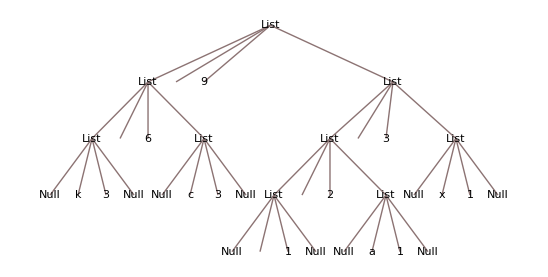

```mathematica
TreeForm[tree2]
```

With only one node, the BinaryPath for tree1 should be an empty list -- there is no information content where there is only a single branch.

```mathematica
BinaryPath[tree1," "]
```

{1}

```mathematica
BinaryPath[tree1,"o"]
```

{0}

```mathematica
BinaryPath[tree2,"a"]
```

{1,0,1}

```mathematica
BinaryPath[tree2,"!"]
```

False

```mathematica
StegDecryptIter[ciphertext_String,cipherpos_Integer,decodedbits_List]:=
If[cipherpos>StringLength[ciphertext],
decodedbits (* cipher has been fully decoded *),
With[{nls=NextLetters[StringTake[ciphertext,{cipherpos-𝔑+1,cipherpos-1}]]
},
Switch[nls,
{},
StegDecryptIter[ciphertext,cipherpos+𝔑-1,decodedbits],
{_},
StegDecryptIter[ciphertext,cipherpos+1,decodedbits],
_,
With[
{bits=BinaryPath[Huffman[nls],
StringTake[ciphertext,{cipherpos}]]
},
Switch[bits,
False,
StegDecryptIter[ciphertext,cipherpos+𝔑-1,decodedbits],
{},
StegDecryptIter[ciphertext,cipherpos+𝔑-1,decodedbits],
_,
StegDecryptIter[ciphertext,cipherpos+1,
Join[decodedbits,bits] ]
]
]
]
]
]
```

```mathematica
StegDecrypt[ciphertext_String]:=
StringJoin[
FromCharacterCode[FromDigits[#,2]]&/@
Partition[
StegDecryptIter[ciphertext,𝔑+1,{}],
16
]
]
```

```mathematica
bits=StegDecryptIter["gGreasy.” RT if wren_McSkend.1 go-",𝔑+1,{}]
```

{1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
Length[bits]
```

38

The text below should match the bits for “hello”.

```mathematica
StegDecryptIter["e_Prohoesnt:d83d:de02 hterned u........I d.",𝔑+1,{}]
```

{0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Partition[
StegDecryptIter["e_Prohoesnt:d83d:de02 hterned u........I d.",𝔑+1,{}],
16]
```

{{0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1}}

```mathematica
StegDecrypt["e_Prohoesnt:d83d:de02 hterned u........I d."]//Timing
```

{19.46122,hello}

```mathematica
StegDecryptIter["ke 3' to psychool anyMight",𝔑+1,{}]
```

{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
Partition[%120,16]
```

{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Partition[ToBinaryString["hello"],16]
```

{{0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1}}

```mathematica
StegEncrypt["abcd"]
```

Kvnt h…Chrispliphoto the wqnS per…

```mathematica
StegDecryptIter[%114,𝔑,{}]
```

Request to Huffman an empty list

$Aborted

```mathematica
NextLetters["e 3'"]
```

{{ ,1}}

```mathematica
Length[{0,1,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1}]
```

27

```mathematica
NextLetters["sy.”"]
```

{{
,1},{ ,4},{R,1}}

### Frequency List for Debugging

```mathematica
freqlist={{"aaa",1},{"aab",2},{"aba",3},{"abb",4},
		{"baa",5},{"bab",6},{"bba",7},{"bbb",8}};
```

```mathematica
𝔑=3;
```

```mathematica
𝔗=freqlist;
```

```mathematica
Partition[ToBinaryString["abbababa"],16]
```

{{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1}}

```mathematica
cipher=StegEncrypt["abbababa"]
```

baaaaaaaaaaabbaaaabaaaaaaaaabbaaabaaaaaaaaaabbaaabaaaaaaaaaabbaaaabaaaaaaaaabbaaabaaaaaaaaaabbaaaabaaaaaaaaabbaaabaaaaaaaaaabbaaaab

```mathematica
bits=StegDecryptIter[cipher,𝔑+1,{}]
```

Request to Huffman a non-list: nls

$Aborted

```mathematica
Length[bits]
```

128

```mathematica
Partition[bits,16]
```

{{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1}}

For a well-behaved ntable (all outputs of NextLetter return a tree, encoding either a 0 or 1), StegEncrypt and StegDecryptIter are correct.

```mathematica
rfreqlist={{"aaa",1},{"aab",2},{"aba",3},{"abb",4},{"bba",5},{"baa",6}};
```

```mathematica
𝔑=3;
```

```mathematica
𝔗=rfreqlist;
```

Because many combinations of a and b do not appear in rfreqlist, the ciphertext size can explode due to many repeated “resets”.

```mathematica
NextLetters["bb"]
```

{{a,5}}

```mathematica
Huffman[NextLetters["bb"]]
```

{Null,a,5,Null}

```mathematica
BinaryPath[Huffman[NextLetters["bb"]],"a"]
```

{}

```mathematica
Huffman[NextLetters["aaa"]]
```

{{Null,a,1,Null},,3,{Null,b,2,Null}}

```mathematica
Huffman[NextLetters["aab"]]
```

{{Null,a,3,Null},,7,{Null,b,4,Null}}

```mathematica
Huffman[NextLetters["aba"]]
```

{Null,a,6,Null}

```mathematica
Huffman[NextLetters["abb"]]
```

{Null,a,5,Null}

```mathematica
Huffman[NextLetters["baa"]]
```

{{Null,a,1,Null},,3,{Null,b,2,Null}}

```mathematica
Huffman[NextLetters["bab"]]
```

{{Null,a,3,Null},,7,{Null,b,4,Null}}

```mathematica
Huffman[NextLetters["bba"]]
```

{Null,a,6,Null}

```mathematica
Huffman[NextLetters["bbb"]]
```

{Null,a,5,Null}

```mathematica
cipher=StegEncrypt["abab"]
```

baaaaaaaaaaabbaaaaaabaaaaaaaaaabbaaaaabaaaaaaaaaaabbaaaaaabaaaaaaaaaabbaaaaaba

```mathematica
Partition[StegDecryptIter[cipher,𝔑+1,{}],16]
```

{{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0}}

This should return {0, 1, 1, 0}:

```mathematica
StegDecryptIter["aaabbaaa",3,{}]
```

{0,1,1,0}

```mathematica
BinaryPath[Huffman[NextLetters["ab"]],"b"]
```

{1}

```mathematica
Length[StegDecryptIter[cipher,𝔑+1,{}]]
```

64

```mathematica
Partition[ToBinaryString["abab"],16]
```

{{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0}}